### 3D, U = 2, Gamma = 0.7

```mathematica
Quit[]
```

```mathematica
hclattice=Import["/Users/lehoanganh/Documents/GitHub/HF_ZGNR/Examples/data/mathematica_3D_lattice_bond_L100W24.txt","Table"]//Flatten;
hcsiteA=Import["/Users/lehoanganh/Documents/GitHub/HF_ZGNR/Examples/data/mathematica_3D_siteA_L100W24.txt","Table"];
hcsiteB=Import["/Users/lehoanganh/Documents/GitHub/HF_ZGNR/Examples/data/mathematica_3D_siteB_L100W24.txt","Table"];
szup=Import["/Users/lehoanganh/Documents/GitHub/HF_ZGNR/Examples/data/mathematica_sz_up_L100W24_U2_g0.7.txt","Table"]//Flatten;
szdn=Import["/Users/lehoanganh/Documents/GitHub/HF_ZGNR/Examples/data/mathematica_sz_dn_L100W24_U2_g0.7.txt","Table"]//Flatten;
```

```mathematica
<<MaTex`
```

```mathematica
Graphics3D[{
{Black,Line@Partition[#,3]&/@Partition[hclattice,6]},
{Black,PointSize[0.006],Point/@Partition[hcsiteA,3]},
{Gray,PointSize[0.006],Point/@Partition[hcsiteB,3]},
{Red,Thick,CapForm["Round"],Line[#]&/@(Partition[#,3]&/@Partition[szup,6])},
{Blue,Thick,CapForm["Round"],Line[#]&/@(Partition[#,3]&/@Partition[szdn,6])}},Axes->True,ImageSize->Large,AxesLabel->{MaTeX["k",Magnification->3],MaTeX["l",Magnification->3],MaTeX["S_z",Magnification->3]},Ticks->{{{0,MaTeX["0",Magnification->2]},{25,MaTeX["25",Magnification->2]},{50,MaTeX["50",Magnification->2]},{75,MaTeX["75",Magnification->2]},{100,MaTeX["100",Magnification->2]}}, {{0.86,MaTeX["1",Magnification->2]},{3.75,MaTeX["8",Magnification->2]},{7.2,MaTeX["16",Magnification->2]},{10.68,MaTeX["24",Magnification->2]}},{{2,MaTeX["0.2",Magnification->2]},{-2,MaTeX["-0.2",Magnification->2]},{0,MaTeX["0",Magnification->2]}}},BaseStyle->{FontSize->18,Black,FontFamily->"Latin Modern Roman" },BoxRatios->{5, 1, 0.8},Boxed->False]
```

-Graphics3D-

### U=3, Gamma=0 3D

```mathematica
hclattice=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_bond.txt","Table"]//Flatten;
hcsiteA=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_site_A.txt","Table"]//Flatten;
hcsiteB=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_site_B.txt","Table"]//Flatten;
szup=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U3_g0_up.txt","Table"]//Flatten;
szdn=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U3_g0_dn.txt","Table"]//Flatten;
```

```mathematica
edge1=Select[(Partition[#,3]&/@Partition[szup,6]),#[[1]][[2]]>10.3&];
edge2=Select[(Partition[#,3]&/@Partition[szup,6]),#[[1]][[2]]<1&];
```

```mathematica
<<MaTeX`
```

```mathematica
Graphics3D[{
{Black,Line@Partition[#,3]&/@Partition[hclattice,6]},
{Black,PointSize[0.006],Point/@Partition[hcsiteA,3]},
{Gray,PointSize[0.006],Point/@Partition[hcsiteB,3]},
{Red,Opacity[1],Thickness[0.01],CapForm["Round"],Line[#]&/@(Partition[#,3]&/@Partition[szup,6])},
{Blue,Opacity[1],Thickness[0.01],CapForm["Round"],Line[#]&/@(Partition[#,3]&/@Partition[szdn,6])}
},
Axes->True,ImageSize->Medium,AxesLabel->{MaTeX["k",Magnification->3],MaTeX["l",Magnification->3],MaTeX["S_z",Magnification->3]},Ticks->{{{1,MaTeX["1",Magnification->2]},{2,MaTeX["2",Magnification->2]},{3,MaTeX["3",Magnification->2]},{25,MaTeX["25",Magnification->2]},{50,MaTeX["50",Magnification->2]},{75,MaTeX["75",Magnification->2]},{100,MaTeX["100",Magnification->2]}}, {{0.86,MaTeX["1",Magnification->2]},{3.75,MaTeX["8",Magnification->2]},{7.2,MaTeX["16",Magnification->2]},{10.68,MaTeX["24",Magnification->2]}},{{0.3,MaTeX["0.3",Magnification->2]},{-0.3,MaTeX["-0.3",Magnification->2]},{0,MaTeX["0",Magnification->2]}}},BaseStyle->{FontSize->18,Black,FontFamily->"Latin Modern Roman" },BoxRatios->{0.3, 1, 0.2},Boxed->False,PlotRange->{{0,3.1},All,All}]
```

-Graphics3D-

### U=5, Gamma=0.1 3D

```mathematica
hclattice=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_bond_L100W64.txt","Table"]//Flatten;
hcsiteA=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_site_A_L100W64.txt","Table"]//Flatten;
hcsiteB=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_site_B_L100W64.txt","Table"]//Flatten;
szup=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U5_g01_up.txt","Table"]//Flatten;
szdn=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U5_g01_dn.txt","Table"]//Flatten;
```

```mathematica
<<MaTex`
```

```mathematica
(Line@Partition[#,3]&/@Partition[hclattice,6])[[Last]]
```

Part::pkspec1: The expression Last cannot be used as a part specification.

{Line[{{1.,28.0014880556968464,0.},{1.5,27.7128129211020351,0.}}],9466,Line[{{100.5,1.15470053837925146,0.},{1}}]}⟦Last⟧
 |  |  |  |

```mathematica
Line[#]&/@(Partition[#,3]&/@Partition[szup,6])//Last
```

Line[{{90.,-16.4544826719043336,0.},{90.,-16.4544826719043336,4.21297022996572323}}]

```mathematica
Graphics3D[{
{Black,Line@Partition[#,3]&/@Partition[hclattice,6]},
{Black,PointSize[0.004],Point/@Partition[hcsiteA,3]},
{Gray,PointSize[0.004],Point/@Partition[hcsiteB,3]},
{Red,Thickness[0.003],CapForm["Round"],Line[#]&/@(Partition[#,3]&/@Partition[szup,6])},
{Blue,Thickness[0.003],CapForm["Round"],Line[#]&/@(Partition[#,3]&/@Partition[szdn,6])}},Axes->True,ImageSize->Medium,AxesLabel->{MaTeX["k",Magnification->3],MaTeX["l",Magnification->3],MaTeX["S_z",Magnification->3]},Ticks->{{{0,MaTeX["0",Magnification->2]},{25,MaTeX["25",Magnification->2]},{50,MaTeX["50",Magnification->2]},{75,MaTeX["75",Magnification->2]},{100,MaTeX["100",Magnification->2]}}, {{0.86,MaTeX["1",Magnification->2]},{14.145,MaTeX["32",Magnification->2]},{27.71281,MaTeX["64",Magnification->2]}},{{4,MaTeX["0.4",Magnification->2]},{-4,MaTeX["-0.4",Magnification->2]},{0,MaTeX["0",Magnification->2]}}},BaseStyle->{FontSize->18,Black,FontFamily->"Latin Modern Roman" },Boxed->False,BoxRatios->{4, 1, 0.2}]
```

### U=5, Gamma=0.1 2D

```mathematica
hclattice=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_bond_L50W32.txt","Table"]//Flatten;
szup=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U5_g0.1_up.txt","Table"]//Flatten,3];
szdn=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U5_g0.1_dn.txt","Table"]//Flatten,3];
(*szup=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U5_g006_up.txt","Table"]//Flatten,3];
szdn=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U5_g006_dn.txt","Table"]//Flatten,3];*)
(*szup=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U6_g6_up.txt","Table"]//Flatten,3];
szdn=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U6_g6_dn.txt","Table"]//Flatten,3];*)
hcsiteA=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_site_A_L50W32.txt","Table"]//Flatten,2];
hcsiteB=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_site_B_L50W32.txt","Table"]//Flatten,2];
```

```mathematica
<<MaTex`
```

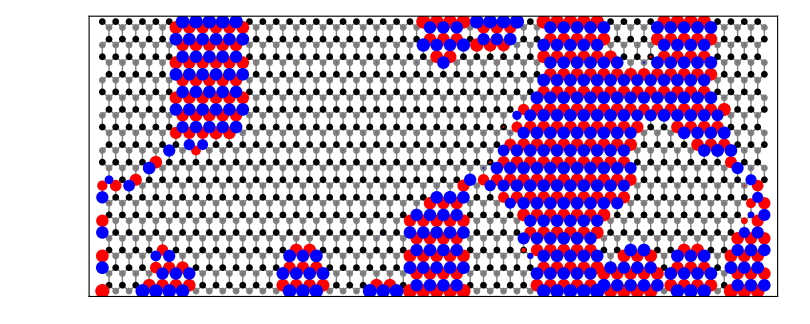

```mathematica
Graphics[{
{Black,Opacity[0.5],Line@Partition[#,2]&/@Partition[hclattice,4]},
{Black,PointSize[0.006],Point/@hcsiteA},{Gray,PointSize[0.006],Point/@hcsiteB},
{Red,PointSize[#[[3]]/35],Point[#[[1;;2]]]}&/@szup,
{Blue,PointSize[Abs[#[[3]]]/35],Point[#[[1;;2]]]}&/@szdn},
Frame->True,
FrameTicks->{{{{0.86,MaTeX["1",Magnification->2]},{3.75,MaTeX["8",Magnification->2]},{7.2,MaTeX["16",Magnification->2]},{10.68,MaTeX["24",Magnification->2]},{14.145,MaTeX["32",Magnification->2]}},None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,50,10]}],None}},
FrameLabel->{MaTeX["k",Magnification->3],MaTeX["l",Magnification->3]}]
```

```mathematica
occupationup=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/n_clean_up_L50W32_U5_gamma0.1.txt","Table"]//Flatten;
occupationdn=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/n_clean_dn_L50W32_U5_gamma0.1.txt","Table"]//Flatten;
```

```mathematica
Graphics[{
{Black,Opacity[0.5],Line@Partition[#,2]&/@Partition[hclattice,4]},
{Black,PointSize[0.006],Point/@hcsiteA},{Gray,PointSize[0.006],Point/@hcsiteB},
{Red,PointSize[#[[3]]/35],Point[#[[1;;2]]]}&/@occupationup},
Frame->True,
FrameTicks->{{{{0.86,MaTeX["1",Magnification->2]},{3.75,MaTeX["8",Magnification->2]},{7.2,MaTeX["16",Magnification->2]},{10.68,MaTeX["24",Magnification->2]},{14.145,MaTeX["32",Magnification->2]}},None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,50,10]}],None}},
FrameLabel->{MaTeX["k",Magnification->3],MaTeX["l",Magnification->3]}]
```

Part::partd: Part specification 0.92552381031641251⟦3⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 2 in 0.92552381031641251.

Part::partd: Part specification 0.925518261261143671⟦3⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 2 in 0.925518261261143671.

Part::partd: Part specification 0.925523638760101797⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in 0.925523638760101797.

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

```mathematica
pos=Flatten[Table[{i,j},{i,1,50},{j,1,32}],1];
plotup=Partition[Flatten[Transpose[{pos,occupationup}]],3];
plotdn=Partition[Flatten[Transpose[{pos,occupationdn}]],3];
```

```mathematica
ListPlot3D[plotup,PlotRange->Full,PlotStyle->Directive[Opacity[1],Red],InterpolationOrder->100,ViewPoint->{2.3, -2.4, 2.},BaseStyle->Directive[FontSize->25,FontColor->Black]]
```

-Graphics3D-

### U=1, Gamma=5 2D

```mathematica
hclattice=Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_bond_L32W8.txt","Table"]//Flatten;
szup=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U1_g5_up.txt","Table"]//Flatten,3];
szdn=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/sz_U1_g5_dn.txt","Table"]//Flatten,3];
(*hcsiteA=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_site_A_L50W32.txt","Table"]//Flatten,2];
hcsiteB=Partition[Import["/Users/lehoanganh/CMPLab/2022.06 Phase diagram of TEE/hc_lattice_site_B_L50W32.txt","Table"]//Flatten,2];*)
```

```mathematica
szup
```

{{1.,3.75277674973256747,3.91751704126308553×10^-6},{2.,3.75277674973256747,8.08444584549095069×10^-6},{3.,3.75277674973256747,0.0000170466646837730274},{4.,3.75277674973256747,0.0000166219440019266251},{5.,3.75277674973256747,8.05087075494981264×10^-6},{6.,3.75277674973256747,1.0108316151752339×10^-6},{8.,3.75277674973256747,8.85273957029752978×10^-7},{9.,3.75277674973256747,3.68096847419563389×10^-6},{10.,3.75277674973256747,3.14363873421541484×10^-6},{11.,3.75277674973256747,2.83656180752323017×10^-7},{12.,3.75277674973256747,1.82992141689597432×10^-7},{13.,3.75277674973256747,1.85915287738425139×10^-6},{14.,3.75277674973256747,4.2106006211406477×10^-6},{15.,3.75277674973256747,3.3362197491837442×10^-6},{16.,3.75277674973256747,1.07244165747921727×10^-6},{18.,3.75277674973256747,1.62547790227840494×10^-7},{19.,3.75277674973256747,2.49851750289131758×10^-7},{20.,3.75277674973256747,8.64811989909064494×10^-7},{21.,3.75277674973256747,1.19876372886573712×10^-6},{22.,3.75277674973256747,5.57259172612178944×10^-7},{23.,3.75277674973256747,7.33273382375054794×10^-7},{24.,3.75277674973256747,3.93762738998271189×10^-7},{25.,3.75277674973256747,7.24695812553965979×10^-7},{26.,3.75277674973256747,1.0570211874116886×10^-6},{27.,3.75277674973256747,4.0955005561893465×10^-7},{31.,3.75277674973256747,3.07635747515133673×10^-7},{32.,3.75277674973256747,1.50671028953386355×10^-6},{11.5,3.46410161513775439,1.7642613209245539×10^-7},{12.5,3.46410161513775439,2.68475872200468757×10^-7},{27.5,3.46410161513775439,7.4266501282060915×10^-9},{28.5,3.46410161513775439,9.95169602280299159×10^-8},{29.5,3.46410161513775439,1.30746889370758623×10^-7},{30.5,3.46410161513775439,3.25219107755181369×10^-8},{1.5,2.8867513459481291,1.53514893008743769×10^-6},{2.5,2.8867513459481291,4.22241240000120754×10^-6},{3.5,2.8867513459481291,1.06668007482380034×10^-6},{4.5,2.8867513459481291,1.53406062042282798×10^-6},{5.5,2.8867513459481291,2.52085209043184655×10^-6},{6.5,2.8867513459481291,1.63960272819840824×10^-6},{7.5,2.8867513459481291,1.59158598408981611×10^-6},{8.5,2.8867513459481291,9.46637262022598236×10^-7},{9.5,2.8867513459481291,3.69503150104977252×10^-7},{10.5,2.8867513459481291,1.12340204799776799×10^-6},{11.5,2.8867513459481291,1.62846690435203279×10^-6},{12.5,2.8867513459481291,1.20432856343111183×10^-6},{13.5,2.8867513459481291,6.86258582016652241×10^-7},{14.5,2.8867513459481291,5.13879125002558723×10^-7},{15.5,2.8867513459481291,8.28701963995204238×10^-7},{16.5,2.8867513459481291,8.29210882680175843×10^-7},{17.5,2.8867513459481291,1.7499160548384296×10^-7},{18.5,2.8867513459481291,7.15092421388341393×10^-8},{19.5,2.8867513459481291,1.42987569229369171×10^-7},{21.5,2.8867513459481291,8.63631595404701358×10^-8},{22.5,2.8867513459481291,1.030565680848472×10^-7},{23.5,2.8867513459481291,1.58476960276932033×10^-7},{24.5,2.8867513459481291,1.5663340449667551×10^-7},{28.5,2.8867513459481291,2.04617417343122554×10^-7},{29.5,2.8867513459481291,2.0437781270143951×10^-7},{31.5,2.8867513459481291,4.07854018336095692×10^-8},{32.5,2.8867513459481291,5.57732438594138458×10^-7},{11.,2.59807621135331601,1.13872858920061049×10^-8},{28.,2.59807621135331601,3.89915265075480022×10^-8},{29.,2.59807621135331601,1.20669459591216111×10^-7},{30.,2.59807621135331601,1.2713678451681254×10^-7},{1.,2.02072594216369028,5.50776891317106276×10^-7},{2.,2.02072594216369028,1.1721472535919375×10^-6},{3.,2.02072594216369028,3.26086085161714223×10^-6},{4.,2.02072594216369028,1.74899366517378141×10^-6},{6.,2.02072594216369028,6.76714679848089418×10^-8},{7.,2.02072594216369028,5.84882288434673825×10^-7},{8.,2.02072594216369028,7.75068105252074702×10^-7},{9.,2.02072594216369028,8.84753312307973161×10^-7},{10.,2.02072594216369028,1.74638750066735682×10^-6},{11.,2.02072594216369028,5.46028552483868168×10^-7},{12.,2.02072594216369028,8.00749230422947989×10^-7},{13.,2.02072594216369028,1.11760267873517449×10^-6},{14.,2.02072594216369028,1.20475823983667851×10^-6},{15.,2.02072594216369028,4.19786907457364578×10^-7},{16.,2.02072594216369028,4.16080146226072145×10^-7},{17.,2.02072594216369028,5.21590229785040549×10^-7},{18.,2.02072594216369028,1.98739017021054565×10^-7},{19.,2.02072594216369028,2.06521679757543097×10^-8},{21.,2.02072594216369028,3.87400980739194267×10^-9},{22.,2.02072594216369028,2.33800107052317685×10^-8},{23.,2.02072594216369028,5.07332353905098898×10^-9},{25.,2.02072594216369028,2.00883590872891205×10^-8},{26.,2.02072594216369028,1.20689318039435278×10^-7},{27.,2.02072594216369028,8.54309823994370277×10^-8},{28.,2.02072594216369028,2.53660318583204258×10^-8},{30.,2.02072594216369028,4.95014111645541988×10^-8},{31.,2.02072594216369028,4.01941754712975552×10^-7},{32.,2.02072594216369028,3.18540521127008702×10^-7},{2.5,1.73205080756887719,6.93545971097719871×10^-7},{18.5,1.73205080756887719,1.80071416056026834×10^-7},{29.5,1.73205080756887719,7.77136194840544192×10^-8},{30.5,1.73205080756887719,5.36165080833317376×10^-7},{31.5,1.73205080756887719,2.00262768590420137×10^-8},{1.5,1.15470053837925146,2.24070033083556552×10^-7},{2.5,1.15470053837925146,4.43926383930648427×10^-7},{3.5,1.15470053837925146,7.02758567894257169×10^-7},{4.5,1.15470053837925146,1.0780996801962317×10^-6},{5.5,1.15470053837925146,1.39268347659760039×10^-6},{6.5,1.15470053837925146,1.47706763575783384×10^-6},{7.5,1.15470053837925146,1.27943142014252942×10^-6},{8.5,1.15470053837925146,1.02554890824002598×10^-6},{9.5,1.15470053837925146,9.30492192241505478×10^-7},{10.5,1.15470053837925146,1.29642155438647322×10^-6},{11.5,1.15470053837925146,1.279652681457355×10^-6},{12.5,1.15470053837925146,1.98229211306744091×10^-6},{13.5,1.15470053837925146,2.15181498686156658×10^-6},{14.5,1.15470053837925146,1.7321012948934289×10^-6},{15.5,1.15470053837925146,1.15268315586947168×10^-6},{16.5,1.15470053837925146,8.16843649525944571×10^-7},{19.5,1.15470053837925146,6.25563384426541802×10^-9},{21.5,1.15470053837925146,7.85265197311701968×10^-9},{22.5,1.15470053837925146,1.55264330836679676×10^-8},{23.5,1.15470053837925146,2.36326841429601586×10^-8},{24.5,1.15470053837925146,2.15688653049106449×10^-8},{25.5,1.15470053837925146,3.12402604341066592×10^-8},{26.5,1.15470053837925146,4.22113452525074706×10^-8},{27.5,1.15470053837925146,5.95583962981205417×10^-8},{28.5,1.15470053837925146,1.51481669791175833×10^-7},{29.5,1.15470053837925146,3.00204430508932418×10^-7},{30.5,1.15470053837925146,3.53869176294985266×10^-7},{31.5,1.15470053837925146,3.06006610051312578×10^-7},{32.5,1.15470053837925146,1.8835404314021531×10^-7},{1.,0.866025403784438597,1.30324064079312407×10^-6},{10.,0.866025403784438597,4.6912227843337595×10^-7},{17.,0.866025403784438597,1.71217114042221397×10^-7},{18.,0.866025403784438597,2.96913794384234819×10^-7},{19.,0.866025403784438597,1.25192425159958987×10^-6},{20.,0.866025403784438597,1.41763442235154358×10^-7},{26.,0.866025403784438597,3.50782339980648672×10^-9},{32.,0.866025403784438597,1.53986486209345408×10^-6}}

```mathematica
<<MaTex`
```

```mathematica
(Line@Partition[#,3]&/@Partition[hclattice,6])[[Last]]
```

Part::pkspec1: The expression Last cannot be used as a part specification.

{Line[{{1.,28.0014880556968464,0.},{1.5,27.7128129211020351,0.}}],9466,Line[{{100.5,1.15470053837925146,0.},{1}}]}⟦Last⟧
 |  |  |  |

```mathematica
Line[#]&/@(Partition[#,3]&/@Partition[szup,6])//Last
```

Line[{{90.,-16.4544826719043336,0.},{90.,-16.4544826719043336,4.21297022996572323}}]

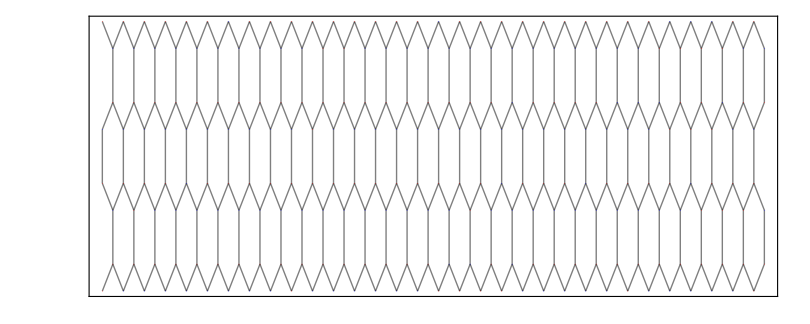

```mathematica
Graphics[{
{Black,Opacity[0.5],Line@Partition[#,2]&/@Partition[hclattice,4]}(*,
{Black,PointSize[0.006],Point/@hcsiteA},{Gray,PointSize[0.006],Point/@hcsiteB}*),
{Red,PointSize[#[[3]]/5],Point[#[[1;;2]]]}&/@szup,
{Blue,PointSize[Abs[#[[3]]]/5],Point[#[[1;;2]]]}&/@szdn},
Frame->True,
FrameTicks->{{{{0.86,MaTeX["1",Magnification->2]},{3.75,MaTeX["8",Magnification->2]},{7.2,MaTeX["16",Magnification->2]},{10.68,MaTeX["24",Magnification->2]},{14.145,MaTeX["32",Magnification->2]}},None},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->2]},{x,Range[0,50,10]}],None}},
FrameLabel->{MaTeX["k",Magnification->3],MaTeX["l",Magnification->3]}]
```